Set::write: Tag Plus in Fm1 - Fm15 is Protected.

1
2
3
4
5

ListPlot::nonopt: Options expected (instead of 0.424676
0.318421
0.256396
0.215758
0.187024) beyond position 1 in ListPlot[TagBox[GridBox[{{. An option must be a rule or a list of rules.

ListPlot[1
2
3
4
5,0.424676
0.318421
0.256396
0.215758
0.187024]

∞::indet: Indeterminate expression 0.` ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.` encountered.

∞::indet: Indeterminate expression -3.` + ComplexInfinity + ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.` encountered.

∞::indet: Indeterminate expression -3.` + ComplexInfinity + ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.` encountered.

∞::indet: Indeterminate expression 0.` ComplexInfinity encountered.

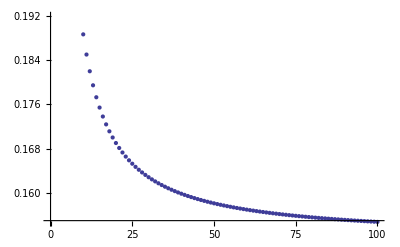

Indeterminate
0.33255
0.278916
0.248346
0.228897
0.215578
0.205958
0.198722
0.193103
0.188627
0.184985
0.181968
0.179432
0.177273
0.175413
0.173796
0.172378
0.171125
0.170011
0.169013
0.168115
0.167303
0.166565
0.165892
0.165275
0.164709
0.164186
0.163703
0.163255
0.162838
0.162449
0.162086
0.161746
0.161428
0.161128
0.160846
0.160579
0.160328
0.16009
0.159864
0.15965
0.159447
0.159254
0.15907
0.158894
0.158726
0.158566
0.158413
0.158266
0.158126
0.157991
0.157862
0.157738
0.157618
0.157503
0.157393
0.157286
0.157183
0.157084
0.156989
0.156896
0.156807
0.156721
0.156637
0.156556
0.156478
0.156402
0.156329
0.156257
0.156188
0.156121
0.156056
0.155992
0.15593
0.155871
0.155812
0.155756
0.1557
0.155647
0.155594
0.155543
0.155493
0.155445
0.155398
0.155351
0.155306
0.155262
0.155219
0.155177
0.155136
0.155096
0.155057
0.155019
0.154981
0.154945
0.154909
0.154874
0.15484
0.154806
0.154773

1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80
81
82
83
84
85
86
87
88
89
90
91
92
93
94
95
96
97
98
99
100

```mathematica
Notations;
L=a/b;
d=κb;
c=κa;
a=λa;
b=λb;
bts1=β/b;
bts2=β/a;
Fm1-Fm15=Terms in equation (22) and μ_add of Supplementary-A;
Sig=scaled sigma;





L=0.5;
d=Table[i,{i,1,5,1}];
c=d*L;
b=1.001;
a=b*L;
w=c+a;
x=c-a;
y=d+b;
z=d-b;
bts1=0;
bts2=(bts1/L);
E3d=ExpIntegralE[3,d];
E5d=ExpIntegralE[5,d];
E3c=ExpIntegralE[3,c];
E5c=ExpIntegralE[5,c];
E3w=ExpIntegralE[3,w];
E5w=ExpIntegralE[5,w];
E3x=ExpIntegralE[3,x];
E5x=ExpIntegralE[5,x];
E3y=ExpIntegralE[3,y];
E5y=ExpIntegralE[5,y];
E3z=ExpIntegralE[3,z];
E5z=ExpIntegralE[5,z];

L11=((1.5*L)/(b*b))-((1.5*L*L)/(b*b));
L12=((0.5*L*L*L)+1.0-(0.5*L*L*L*L*bts2)-(L*bts2)+(1.5*L*L*L*bts2)+(3.0*bts2));
L13=(1.0/(1.0+(2.0*bts2)));
L14=(L11*Cosh[b-a])+(L12*L13*Cosh[b-a]);
L15=((1.5*L)/(b*b))-(1.5*L*L);
L16=(0.5*L*L*L)+1.0 -(0.5* L*L*bts2*a*a)-(a*b*bts2);
L17=(1.5*L*L*L*bts2)+(3.0*bts2);
L18=(L15*((Sinh[b-a])/b))+((L16+L17)*L13*((Sinh[b-a])/b));
L1=L14-L18;

L21=(1.5*L*L*(1.0/(a*b)))+(0.5*L*L*L)+1.0+((3.0*L*bts2)/(b*b));
L22=(1.5*L*L*L*bts2)+(3.0*bts2);
L23=(1.0/(1.0+(2.0*bts2)));
L24=((L21*L23)+(L22*L23))*Cosh[b-a];
L25=((1.5*L*L )+(3.0*L*L*bts2)+(a*b*bts2)+(0.5*a*a*L*L*bts2));
L26=(L25*L23)*((Sinh[b-a])/b);
L27=-((1.5*L*L)*(1/(a*b)))-((4.5*L*bts2)*(1.0/(b*b)));
L28=(1.5*L*bts2)*(1.0/(b*b));
L29=(L27*L23)+(L28*L23);
L2=L24+L26+L29;

L31=1.0+(3.0*bts2)-(L*bts2);
L32=(1.0/(1.0+(2.0*bts2)));
L33=(L31*L32)*Cosh[b-a];
L34=(1.0+(3.0*bts2)-(a*b*bts2));
L35=(L34*L32)*((Sinh[b-a])/b);
L3=L33-L35-L;

L41= 1.0+((3.0*bts2)/(a*b))-bts2;
L42=(1.0/(1.0+(2.0*bts2)));
L43=(L41*L42)*Sinh[b-a];
L44=(1.0/b)+((3.0*bts2)/a)-(bts2/b);
L45=(L44*L42)*Cosh[b-a];
L46=((2.0/3.0)*(b/L))+((1.0/3.0)*a*L);
L47=L46*L42;
L4=L43-L45+L47+(1.0/b);

L51=((1.5*L*L) -(1.5*L));
L52=L51*Cosh[b-a];
L53=( (1.5*L*(1.0/b))-(1.5*L*a));
L54=L53*Sinh[b-a];
L55=(a*b)+(0.5*L*L*a*a);
L5=L52+L54-L55;

Fm1=(1.0/6.0)*c*c*L*L*Exp[c]*(E3d-(3.0*(1.0-(2.0/3.0)*(L2/L1)+2.0*(L3/(b*b*L1))))*E5d);
Fm2=(3.0/4.0)*c*c*((L3+L4)/(b*b*b*L1))*Exp[w]*(((c/3.0)*(E3w-L*L*E3y))-((1.0/a)*(E5w-L*L*L*L*E5y)));
Fm3=-(3.0/4.0)*c*c*((L3-L4)/(b*b*b*L1))*Exp[x]*(((c/3.0)*(E3x-L*L*E3z))+((1.0/a)*(E5x-L*L*L*L*E5z)));
Fm4=(c*c/(a*a))*(1.0-L3/L1)*Exp[c]*(E5c-(L*L*L*L*E5d));
Fm5=-(1.0/2.0)*c*c*((L3+L4)/(b*b*b*L1))*(((1.0/b)*(1.0+L*L*L*0.5)+(c/w) )*Exp[-(y-w)]-(1.5/a)-c/w);
Fm6=-(1.0/2.0)*c*c*((L3-L4)/(b*b*b*L1))*(((1.0/b)*(1.0+L*L*L*0.5)-(c/x) )*Exp[-(z-x)]-(1.5/a)+c/x);
Fm7=(c*c/(a*a))*(L3/L1-1.0+(0.5*L*L*L*L3/L1)*(1.0+2.0/c+2.0/(c*c)));
Fm8=-(2.0*c/3.0)*(1.0-((L2/L1)*(1.0+1.0/d))-((d/(b*b))*(1.0+(0.5*L*L*L))))*Exp[-(d-c)];

Fm91=-0.5*d*d*(bts2/(1.0+(2.0*bts2)))*(L5/L1)*(1.0/(b*b))*((3.0/(b*b))+(L/b))*Exp[x];
Fm92=((1.0/3.0)*c*(E3x-L*L*E3z))+((1.0/a)*(E5x-L*L*L*L*E5z));
Fm9=Fm91*Fm92;

Fm101=-0.5*d*d*(bts2/(1.0+(2.0*bts2)))*(L5/L1)*(1.0/(b*b))*((3.0/(b*b))-(L/b))*Exp[w];
Fm102=((1.0/3.0)*c*(E3w-L*L*E3y))-((1.0/a)*(E5w-L*L*L*L*E5y));
Fm10=Fm101*Fm102;

Fm111=(1.0/3.0)*d*d*(bts2/(1.0+(2.0*bts2)))*(L5/L1)*(1.0/(b*b));
Fm112=((3.0/(b*b))+(L/b))*(d/(d-b))*(Exp[-(z-x)]-1.0);
Fm11=Fm111*Fm112;

Fm121=(1.0/3.0)*d*d*(bts2/(1.0+(2.0*bts2)))*(L5/L1)*(1.0/(b*b));
Fm122=((3.0/(b*b))-(L/b))*(d/(d+b))*(Exp[-(y-w)]-1.0);
Fm12=Fm121*Fm122;

Fm131=-(1.0/3.0)*d*d*(bts2/(1.0+(2.0*bts2)))*(L5/L1)*(1.0/(b*b));
Fm132=((3.0/(b*b*b))+(L/(b*b)))*(1.0+(0.5*L*L*L))*Exp[-(z-x)];
Fm13=Fm131*Fm132;

Fm141=-(1.0/3.0)*d*d*(bts2/(1.0+(2.0*bts2)))*(L5/L1)*(1.0/(b*b));
Fm142=((L/(b*b))-(3.0/(b*b*b)))*(1.0+(0.5*L*L*L))*Exp[-(y-w)];
Fm14=Fm141*Fm142;

Fm15=d*d*(L5/L1)*(bts2/(1.0+(2.0*bts2)))*(1.0/(b*b*b*b));

Sig=2.052;
zetas=((Sig*L)/(1+c));
zetas1=zetas;
Data1=Column[Re[zetas*(Fm1+Fm2+Fm3+Fm4+Fm5+Fm6+Fm7+Fm8+Fm9+Fm10+Fm11+Fm12+Fm13+Fm14+Fm15)]];
Data2=Column[d]
ListPlot[Data2,Data1]
```